## Plots para m finito

Como preciso gerar diversos plots, fiz um programa para a plotagem.
1o Grupo de Parâmetros μ=15 m=200 M=10 r=1 q=1.

```mathematica
μ=10;
Clear[m,Energy,A];
Energy[m_]= -p((p^2 √(p^2+  m^2))/((1/μ+p)√(p^2+  m^2)-p^2))(ⅇ^(-A p)/p - ⅇ^(-A √(p^2+  m^2))/(√(p^2+  m^2)))^2
Der[m_]=-(2 (-ⅇ^(-A p)+ⅇ^(-A √(m^2+p^2))) p^3 √(m^2+p^2) (ⅇ^(-A p)/p-(ⅇ^(-A √(m^2+p^2)))/(√(m^2+p^2))))/(-p^2+√(m^2+p^2) (p+1/μ))
FInt[m_]:=NIntegrate[-Der[m],{p,0,∞}, AccuracyGoal->10]
FinalEnergy[m_]:=NIntegrate[Energy[m],{p,0,∞}, AccuracyGoal->10];
```

-(p^3 √(m^2+p^2) (ⅇ^(-A p)/p-(ⅇ^(-A √(m^2+p^2)))/(√(m^2+p^2)))^2)/(-p^2+(1/10+p) √(m^2+p^2))

-(2 (-ⅇ^(-A p)+ⅇ^(-A √(m^2+p^2))) p^3 √(m^2+p^2) (ⅇ^(-A p)/p-(ⅇ^(-A √(m^2+p^2)))/(√(m^2+p^2))))/(-p^2+(1/10+p) √(m^2+p^2))

#### Multiple Values m Plot Energy

```mathematica
μ=10;
mList={12,14,15,16};
color={Red,Purple,Blue,Gray};
SetDirectory[NotebookDirectory[]];
For[n=1,n<=4 ,n=n+1,
m=mList[[n]];
Ep[m]=Plot [FinalEnergy[m],{A,0,1}, PlotRange->{{0,0.5},{0,-17}},
Frame->True,
(*PlotLabel->"Energy as function of distance",*)
FrameLabel->{"a","E (8πq^-2)"} ,
PlotStyle->{color[[n]],Thickness[0.004]},AxesOrigin->{0,0}
(*PlotLegends->Placed[LineLegend[
{"Podolsky mass - m="<>ToString[m]<>""},LabelStyle->{FontSize->8}],{Right,Bottom}]*)]];
```

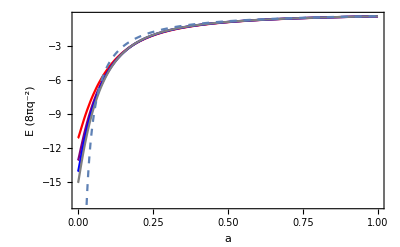

```mathematica
Show[Ep[12],Ep[14],Ep[15],Ep[16],Ep[∞]]
```

#### Force: Derivative of Energy

```mathematica
Der[m_]=D[ Energy[m],A] 
(*Here, energy is derivated with the position*)
```

-(2 (-ⅇ^(-A p)+ⅇ^(-A √(m^2+p^2))) p^3 √(m^2+p^2) (ⅇ^(-A p)/p-(ⅇ^(-A √(m^2+p^2)))/(√(m^2+p^2))))/(-p^2+√(m^2+p^2) (p+1/μ))

#### Consistency check: Energy - Integration of Force

```mathematica
En=Integrate[Der[m],A]
```

-(p^3 √(m^2+p^2) (ⅇ^(-2 A p)/p^2+(ⅇ^(-2 A √(m^2+p^2)))/(m^2+p^2)-(2 ⅇ^(-A (p+√(m^2+p^2))))/(p √(m^2+p^2))))/(-p^2+√(m^2+p^2) (p+1/μ))

```mathematica
Simplify[En-Energy[m]]
```

0

#### Consistency check: Energy - Integration of Force

```mathematica
Clear[Q,P,m,μ,A,Der];
Der[m_]=-(2 (-ⅇ^(-A p)+ⅇ^(-A √(m^2+p^2))) p^3 √(m^2+p^2) (ⅇ^(-A p)/p-(ⅇ^(-A √(m^2+p^2)))/(√(m^2+p^2))))/(-p^2+√(m^2+p^2) (p+1/μ))
FInt[m_]:=NIntegrate[-Der[m],{p,0,∞}, AccuracyGoal->10]
```

-(2 (-ⅇ^(-A p)+ⅇ^(-A √(m^2+p^2))) p^3 √(m^2+p^2) (ⅇ^(-A p)/p-(ⅇ^(-A √(m^2+p^2)))/(√(m^2+p^2))))/(-p^2+√(m^2+p^2) (p+1/μ))

#### Multiple Values m Plot Force Plot

```mathematica
μ=15;
mList={12,14,15,16};
color={Red,Purple,Blue,Gray};
SetDirectory[NotebookDirectory[]];
For[n=1,n<=4 ,n=n+1,
m=mList[[n]];
P[m]=Plot [FInt[m],{A,0,1}, PlotRange->{{0,0.5},{0,-200}},
Frame->True,
(*PlotLabel->"Energy as function of distance",*)
FrameLabel->{"a","F(8πq^-2)"} ,
PlotStyle->{color[[n]],Thickness[0.004]},AxesOrigin->{0,0}
(*PlotLegends->Placed[LineLegend[
{"Podolsky mass - m="<>ToString[m]<>""},LabelStyle->{FontSize->8}],{Right,Bottom}]*)]];
```

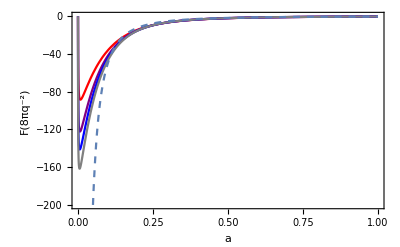

```mathematica
Show[P[12],P[14],P[15],P[16],Q[∞]]
```

#### Plot for Increasing (modulus) Force

```mathematica
mList=Range[5,50,0.5];
```

```mathematica
A=0.01
FInt[mList]
```

0.01

{-13.6452,-17.0466,-20.8043,-24.909,-29.3519,-34.1248,-39.22,-44.6306,-50.3499,-56.3717,-62.6901,-69.2994,-76.1945,-83.37,-90.8211,-98.5429,-106.531,-114.78,-123.287,-132.046,-141.054,-150.306,-159.799,-169.528,-179.489,-189.678,-200.093,-210.727,-221.579,-232.645,-243.92,-255.401,-267.084,-278.967,-291.045,-303.316,-315.775,-328.419,-341.246,-354.251,-367.432,-380.785,-394.308,-407.996,-421.847,-435.858,-450.026,-464.348,-478.82,-493.441,-508.206,-523.114,-538.161,-553.344,-568.661,-584.109,-599.685,-615.386,-631.211,-647.155,-663.217,-679.395,-695.685,-712.084,-728.592,-745.204,-761.919,-778.735,-795.648,-812.656,-829.758,-846.951,-864.232,-881.6,-899.051,-916.585,-934.199,-951.89,-969.657,-987.497,-1005.41,-1023.39,-1041.44,-1059.55,-1077.73,-1095.97,-1114.27,-1132.62,-1151.03,-1169.5,-1188.02}

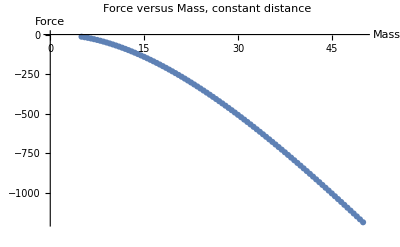

```mathematica
ListPlot[Transpose[{mList,FInt[mList]}],PlotRange->{{0,50},{0,-1188}},AxesLabel->{"Mass","Force"},PlotLabel->"Force versus Mass, constant distance"]
```

#### Plot for two masses

```mathematica
Clear[A]
```

#### Multiple Values m Plot Force Plot

##### 1st way - Energy Plot

```mathematica
μ=15;
mList={12,14,15,16};
color={Red,Purple,Blue,Gray};
SetDirectory[NotebookDirectory[]];
For[n=1,n<=4 ,n=n+1,
m=mList[[n]];
Ep[m]=Plot [FinalEnergy[m],{A,0,1}, PlotRange->{{0.32,0.46},{-1.5,-1}},PlotStyle->{color[[n]],Thickness[0.002]},
Frame->True
(*PlotLabel->"Energy as function of distance",*)
(*FrameLabel->{"a","E 8(πq^2)^-1"} ,*)
];]
```

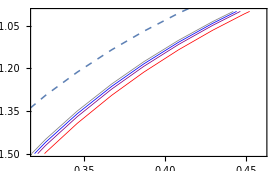

```mathematica
Show[Ep[12],Ep[14],Ep[15],Ep[16],Ep[∞]]
```

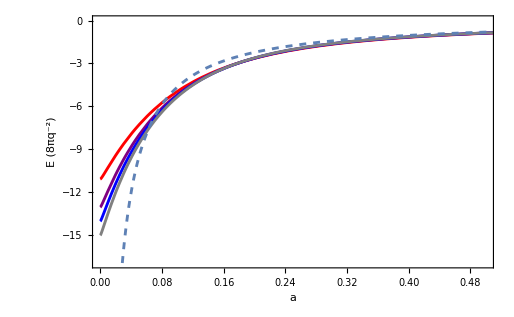

##### 1st way - Force Plot

```mathematica
μ=15;
mList={12,14,15,16};
color={Red,Purple,Blue,Gray};
SetDirectory[NotebookDirectory[]];
For[n=1,n<=4 ,n=n+1,
m=mList[[n]];
P[m]=Plot [FInt[m],{A,0,1}, PlotRange->{{0.4,0.5},{-2,-4}},PlotStyle->{color[[n]],Thickness[0.002]},
Frame->True,
(*PlotLabel->"Energy as function of distance",*)
(*FrameLabel->{"a","E 8(πq^2)^-1"} ,*)
AxesOrigin->{0.4,-2}];]
```

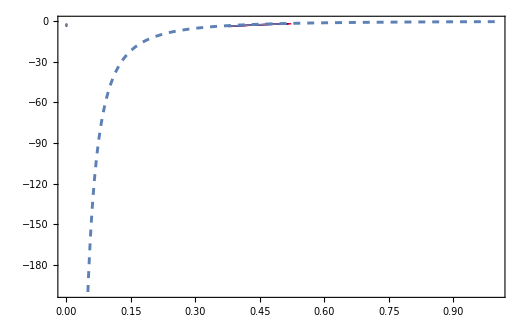

```mathematica
Show[P[12],P[14],P[15],P[16],Q[∞]]
```

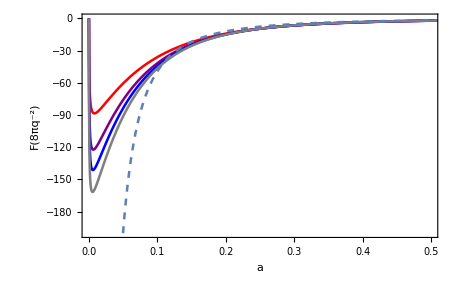

##### 2nd way - Multiple Values m Plot Force Plot

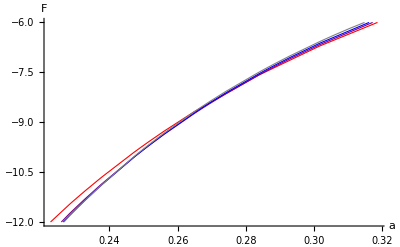

```mathematica
μ=15;
mList={12,14,15,16};
color={Red,Purple,Blue,Gray};
SetDirectory[NotebookDirectory[]];
For[n=1,n<=4 ,n=n+1,
m=mList[[n]];
P[m]=Plot[FInt[m],{A,0.1,1},PlotRange->{{0.22,0.32},{-6,-12}},AxesLabel->{"a","F"} ,PlotStyle->{color[[n]],Thickness[0.002]},PlotLegends->Placed[LineLegend[
{"Podolsky mass - m="<>ToString[m]<>""},LabelStyle->{FontSize->8}],{Right,Bottom}]]];
Show[P[mList[[1]]],P[mList[[2]]],P[mList[[3]]],P[mList[[4]]]]
```

##### 3rd way - Multiple Values m Plot Force Plot

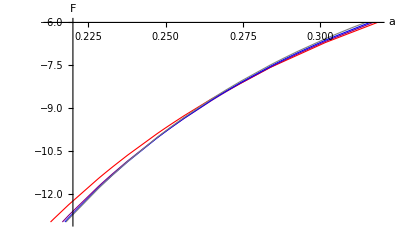

```mathematica
μ=15;
mList={12,14,15,16};
color={Red,Purple,Blue,Gray};
SetDirectory[NotebookDirectory[]];
For[n=1,n<=4 ,n=n+1,
m=mList[[n]];
P[m]=Plot[FInt[m],{A,0.1,1},PlotRange->{{0.22,0.32},{-6,-13}},AxesLabel->{"a","F"} ,PlotStyle->{color[[n]],Thickness[0.002]},
PlotLegends->Placed[LineLegend[
{"Podolsky mass - m="<>ToString[m]<>""},LabelStyle->{FontSize->8}],{Right,Bottom}]]];
Show[P[mList[[1]]],P[mList[[2]]],P[mList[[3]]],P[mList[[4]]]]
```

##### 4th way - Multiple Values m Plot Force Plot

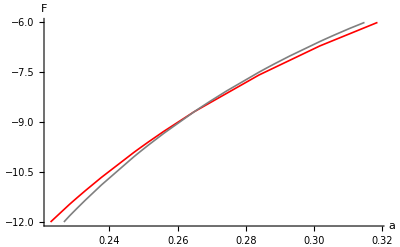

```mathematica
μ=15;
mList={12,14,15,16};
color={Red,Purple,Blue,Gray};
SetDirectory[NotebookDirectory[]];
For[n=1,n<=4 ,n=n+1,
m=mList[[n]];
P[m]=Plot[FInt[m],{A,0.1,1},PlotRange->{{0.22,0.32},{-6,-12}},AxesLabel->{"a","F"} ,PlotStyle->{color[[n]],Thickness[0.003]},PlotLegends->Placed[LineLegend[
{"Podolsky mass - m="<>ToString[m]<>""},LabelStyle->{FontSize->8}],{Right,Bottom}]]];
Show[P[mList[[1]]],P[mList[[4]]]]
```

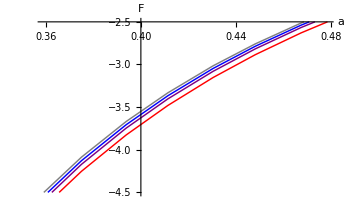

```mathematica
μ=15;
mList={12,14,15,16};
color={Red,Purple,Blue,Gray};
SetDirectory[NotebookDirectory[]];
For[n=1,n<=4 ,n=n+1,
m=mList[[n]];
P[m]=Plot[FInt[m],{A,0.1,1},PlotRange->{{0.40,0.45},{-2.5,-4.5}},AxesLabel->{"a","F"} ,PlotStyle->{color[[n]],Thickness[0.003]},
PlotLegends->Placed[LineLegend[
{"Podolsky mass - m="<>ToString[m]<>""},LabelStyle->{FontSize->8}],{Right,Bottom}]]];
Show[P[mList[[1]]],P[mList[[2]]],P[mList[[3]]],P[mList[[4]]]]
```

##### 5th way - Multiple Values m Plot Force Plot

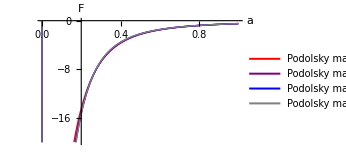

```mathematica
μ=15;
mList={12,14,15,16};
color={Red,Purple,Blue,Gray};
SetDirectory[NotebookDirectory[]];
For[n=1,n<=4 ,n=n+1,
m=mList[[n]];
P[m]=Plot[FInt[m],{A,0,1},PlotRange->{{0.2,0.5},{0,-20}},AxesLabel->{"a","F"} ,PlotStyle->{color[[n]],Thickness[0.004]},PlotLegends->{"Podolsky mass - m="<>ToString[m]<>""}]];
Show[P[mList[[1]]],P[mList[[2]]],P[mList[[3]]],P[mList[[4]]]]
```

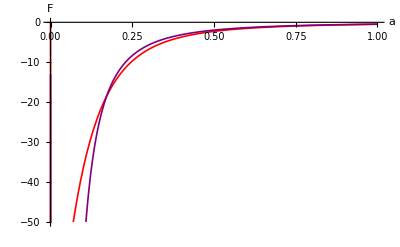

```mathematica
μ=15;
mList={12,60};
color={Red,Purple,Blue,Gray};
SetDirectory[NotebookDirectory[]];
For[n=1,n<=2,n=n+1,
m=mList[[n]];
P[m]=Plot[FInt[m],{A,0,1},PlotRange->{{0,0.5},{0,-50}},AxesLabel->{"a","F"} ,PlotStyle->{color[[n]],Thickness[0.003]},PlotLegends->Placed[LineLegend[
{"Podolsky mass - m="<>ToString[m]<>""},LabelStyle->{FontSize->8}],{Right,Bottom}]]]
Show[P[mList[[1]]],P[mList[[-1]]]]
```

#### Limit case m→∞

##### Energy

```mathematica
LimE=Limit[Energy[mm],mm->∞]
```

ConditionalExpression[-(ⅇ^(-2 A p) p)/(1/10+p), (p^3|p^2|ⅇ^(-A p)/p|p)∈ℝ&&A>0]

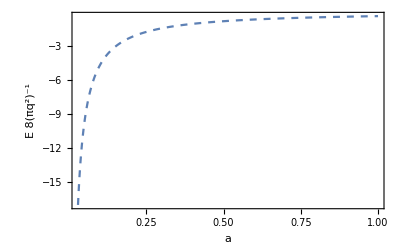

```mathematica
Ep[∞]=Plot [NIntegrate[LimE,{p,0,∞}, AccuracyGoal->10],{A,0,1}, PlotRange->{{0,0.5},{0,-17}},
Frame->True,
(*PlotLabel->"Energy as function of distance",*)
FrameLabel->{"a","E 8(πq^2)^-1"} ,
PlotStyle->{Dashed,Thickness[0.004]},AxesOrigin->{0,0}]
```

##### Force

```mathematica
Clear[m]
Lim=Limit[-Der[m],m-> ∞]
```

ConditionalExpression[-(2 ⅇ^(-2 A p) p^2)/(1/10+p), ]

```mathematica
FIntinf:=NIntegrate[-(2 ⅇ^(-2 A p) p^2)/(p+1/μ),{p,0,∞}, AccuracyGoal->10]
μ=15;
Q[∞]=Plot [FIntinf,{A,0,1}, PlotRange->{{0,0.5},{0,-200}},
Frame->True,
(*PlotLabel->"Energy as function of distance",*)
FrameLabel->{"a","F(8πq^-2)"} ,
PlotStyle->{Dashed,Thickness[0.004]},AxesOrigin->{0,0}];
```

```mathematica
Export["force multiple podolsky masses.pdf",Show[Q[12],Q[14],Q[15],Q[16],Q[∞]]]
```

force multiple podolsky masses.pdf

```mathematica
Clear[m,A,μ]
f=-D[-p(p^2 √(p^2+  m^2))/((1/μ+p)√(p^2+  m^2)-p^2)(ⅇ^(-A p)/p - (ⅇ^(-A √(p^2+  m^2)))/(√(p^2+  m^2)))^2,A]
```

$Aborted

(2 (-ⅇ^(-A p)+ⅇ^(-A √(m^2+p^2))) p^3 √(m^2+p^2) (ⅇ^(-A p)/p-(ⅇ^(-A √(m^2+p^2)))/(√(m^2+p^2))))/(-p^2+√(m^2+p^2) (p+1/μ))

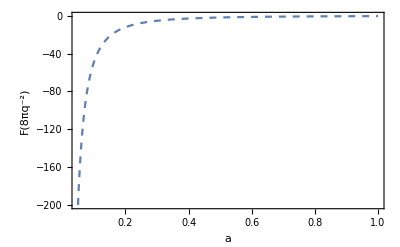

```mathematica
Q[∞]
```

```mathematica
μ=10
m=100 
A=1 

SetDirectory[NotebookDirectory[]]
i=0
For[m=20,m<100,If[m<50,m=m+2,m=m+100],
i=i+1;
If[OddQ[i],If[IntegerQ[i/3],color=Red,color=Purple],If[IntegerQ[i/4],color=Blue,color=Gray]];
Export ["vet-mvariantf"<>ToString[CForm[m]]<>".eps",P[m]=Plot [NIntegrate[ f,{p,0,∞}, AccuracyGoal->5],{A,0,0.5}, PlotRange->{{0,0.06},All},AxesLabel->{a,F/(λ^2/(8π)) } ,PlotStyle->{color,Thickness[0.004]},AxesOrigin->{0,0}]
]
]
```

10

100

1

C:\Users\evers\Documents\Arquivos Everson\Estudos\Artigos\Lee-Wick Semi-Transparent Vectorial\Força\1- m variante

0

```mathematica
Export["vet-variantm0f.eps",Show[P[20],P[22],P[40],P[50],PlotLabel-> "Plotagens para diferentes massas de Podolsky"]]
```

vet-variantm0f.eps

```mathematica
Export["vet-variantm0f.eps",Show[P[32],P[36],P[38],P[50],PlotLabel-> "Plots for different Podolsky masses"]]
```

vet-variantm0f.eps

```mathematica
m=40
Export ["vet-mvariantf"<>ToString[CForm[m]]<>".eps",P[m]=Plot [NIntegrate[ f,{p,0,∞}, AccuracyGoal->5],{A,0,0.5}, PlotRange->{{0,0.1},All},AxesLabel->{a,F/(λ^2/(8π)) } ,PlotStyle->Red,AxesOrigin->{0,0}]
]
```

40

vet-mvariantf40.eps

```mathematica
μ=10
m=100 
A=1 

SetDirectory[NotebookDirectory[]]
i=0
For[m=10,m<18,m=m+2,
i=i+1;
If[OddQ[i],If[IntegerQ[i/3],color=Red,color=Purple],If[IntegerQ[i/4],color=Blue,color=Gray]];
Export ["vet-mvariantf"<>ToString[CForm[m]]<>".eps",P[m]=Plot [NIntegrate[ f,{p,0,∞}, AccuracyGoal->5],{A,0,0.5}, PlotRange->{{0,0.06},All},AxesLabel->{a,F/(λ^2/(8π)) } ,PlotStyle->{color,Thickness[0.004]},AxesOrigin->{0,0}]
]
]
```

10

100

1

C:\Users\evers\Documents\Arquivos Everson\Estudos\Mestrado\Dissertação\Cálculos\8,9- Soluções em Quadraturas\9-Vetorial\Plot Automatizado\Força\1- m variante

0

```mathematica
Export["vet-variantm0f.eps",Show[P[10],P[12],P[14],P[16],PlotLabel-> "Plotagens para diferentes massas de Podolsky"]]
```

vet-variantm0f.eps